```mathematica
Q[kx_,ky_]:=Block[{Δ1,Δ2,Δk,Δks,ξk,dk,t,A,B,M,μ},Δk=Δ1*(Cos[kx]-Cos[ky])+I*Δ2*Sin[kx]*Sin[ky];Δks=Δ1*(Cos[kx]-Cos[ky])-I*Δ2*Sin[kx]*Sin[ky];ξk=-2*t*(Cos[kx]+Cos[ky])-μ;dk={A*Sin[kx],A*Sin[ky],2B*(Cos[kx]+Cos[ky]-2)+M};Δk*Δks+ξk^2-dk.dk]
```

```mathematica
Q[0,π]
```

-(-4 B+M)^2+4 Δ1^2+μ^2

```mathematica
Q[π,0]
```

-(-4 B+M)^2+4 Δ1^2+μ^2

```mathematica
Q[π,π]
```

-(-8 B+M)^2+(4 t-μ)^2

```mathematica
Q[0,0]
```

-M^2+(-4 t-μ)^2

```mathematica
(Q[0,0]*Q[π,π])/(Q[0,π]Q[π,0])/.{B->0,M->0,t->1,μ->0,Δ1->1}
```

16

```mathematica
(Q[0,0]*Q[π,π])/(Q[0,π]Q[π,0])
```

((-M^2+(-4 t-μ)^2) (-(-8 B+M)^2+(4 t-μ)^2))/((-(-4 B+M)^2+4 Δ1^2+μ^2)^2)

```mathematica
Log[-1]
```

ⅈ π

```mathematica
Sign[Q[π,π]*Q[0,0]]/.{μ->0,M->0.8,t->1}
```

Sign[16-(0.8-8 B)^2]

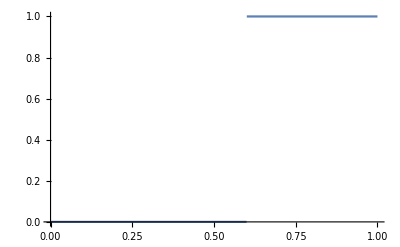

```mathematica
Plot[1/(I π)Log[Sign[16-(0.8-8 B)^2]],{B,0,1}]
```

```mathematica
Sign[-1]
```

-1

```mathematica
Subscript[Δ, 1](Cos[kx]-Cos[ky])+I*Subscript[Δ, 2]*Sin[kx]Sin[ky]//TrigToExp//Expand
```

1/2 ⅇ^(-ⅈ kx) Δ_1+1/2 ⅇ^(ⅈ kx) Δ_1-1/2 ⅇ^(-ⅈ ky) Δ_1-1/2 ⅇ^(ⅈ ky) Δ_1-1/4 ⅈ ⅇ^(-ⅈ kx-ⅈ ky) Δ_2+1/4 ⅈ ⅇ^(ⅈ kx-ⅈ ky) Δ_2+1/4 ⅈ ⅇ^(-ⅈ kx+ⅈ ky) Δ_2-1/4 ⅈ ⅇ^(ⅈ kx+ⅈ ky) Δ_2

```mathematica
Subscript[Δ, 1](Cos[kx]-Cos[ky])+I*Subscript[Δ, 2]*Sin[kx]Sin[ky]/.{Subscript[Δ, 1]->1,Subscript[Δ, 2]->1}
```

Cos[kx]-Cos[ky]+ⅈ Sin[kx] Sin[ky]

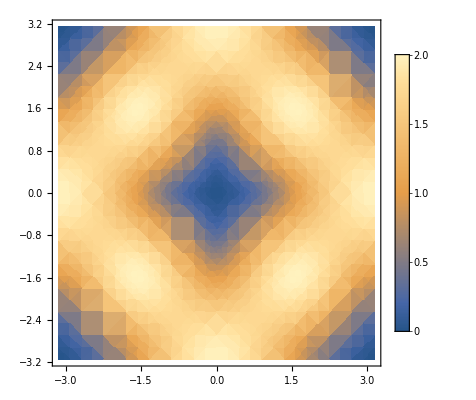

```mathematica
DensityPlot[Abs[Subscript[Δ, 1](Cos[kx]-Cos[ky])+I*Subscript[Δ, 2]*Sin[kx]Sin[ky]/.{Subscript[Δ, 1]->1,Subscript[Δ, 2]->2}],{kx,-π,π},{ky,-π,π},PlotLegends->Automatic]
```

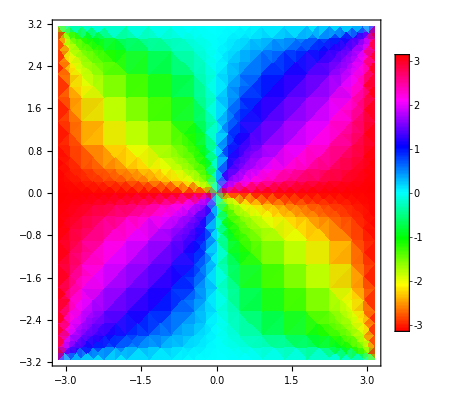

```mathematica
DensityPlot[Arg[Subscript[Δ, 1](Cos[kx]-Cos[ky])+I*Subscript[Δ, 2]*Sin[kx]Sin[ky]/.{Subscript[Δ, 1]->1,Subscript[Δ, 2]->2}],{kx,-π,π},{ky,-π,π},PlotLegends->Automatic,ColorFunction->(Hue[Rescale[#,{-π,π},{0,1}]]&),ColorFunctionScaling->False]
```